```mathematica
CFT 3 states with the first one fixed
```

```mathematica
z derivatives of blocks
```

```mathematica
(*maxium delta moves to the right very fast as der order increase*)
```

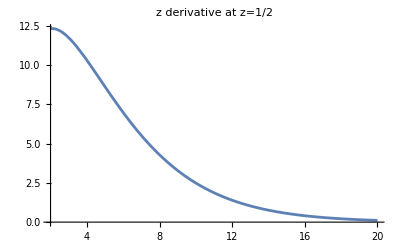

```mathematica
Plot[Table[D[Simplify[crossingEq[1]/.Abs[-1+z]->(1-z),0<z<1/2],{z,n},C[1]]/n!/.z->1/2/.Δσ->-4/10/.s[1]->0,{n,1,1,2}]//Evaluate,{Δ[1],2,20},PlotLabel->"z derivative at z=1/2"]
```

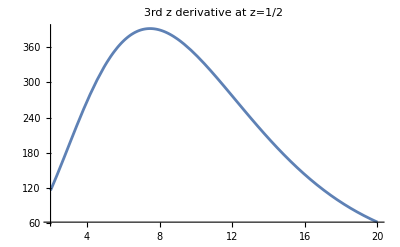

```mathematica
Plot[Table[D[Simplify[crossingEq[1]/.Abs[-1+z]->(1-z),0<z<1/2],{z,n},C[1]]/n!/.z->1/2/.Δσ->-4/10/.s[1]->0,{n,3,3,2}]//Evaluate,{Δ[1],2,20},PlotLabel->"3rd z derivative at z=1/2"]
```

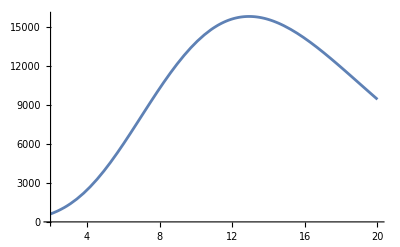

```mathematica
Plot[Table[D[Simplify[crossingEq[1]/.Abs[-1+z]->(1-z),0<z<1/2],{z,n},C[1]]/n!/.z->1/2/.Δσ->-4/10/.s[1]->0,{n,5,5,2}]//Evaluate,{Δ[1],2,20}]
```

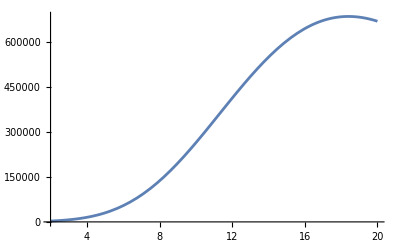

```mathematica
Plot[Table[D[Simplify[crossingEq[1]/.Abs[-1+z]->(1-z),0<z<1/2],{z,n},C[1]]/n!/.z->1/2/.Δσ->-4/10/.s[1]->0,{n,7,7,2}]//Evaluate,{Δ[1],2,20}]
```

```mathematica
new z sampling
```

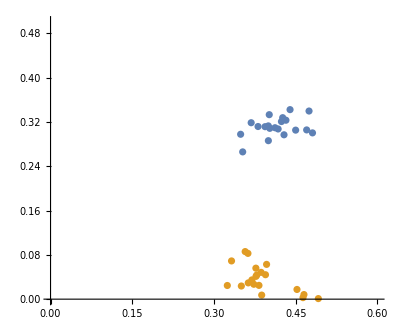

```mathematica
Plot[Table[C[3]/.Solve[crossingEq[3]==0/.Δσ->-4/10/.Δ[i_]->{-4/10,2+d2,36/10+d3,76/10}[[i]]/.s[i_]->{0,2,4,0}[[i]]/.C[1]->-3.65312/.{z->zcomplex[Sqrt[RandomReal[{0,1}]((35/100)^2-(3/10)^2)+(3/10)^2],RandomReal[{1,Pi/2}]]}//N,C[3]][[1]]//Chop,10]/. C[2]->x//Evaluate,{x,-.05,.01}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

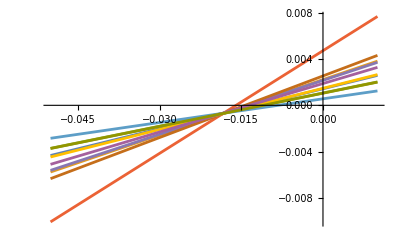

```mathematica
blue points
```

```mathematica
orange points
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

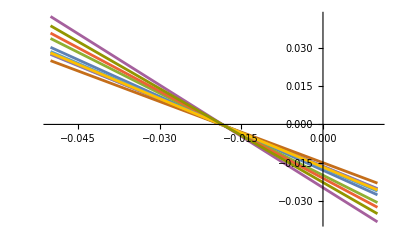

```mathematica
Plot[Table[C[3]/.Solve[crossingEq[3]==0/.Δσ->-4/10/.Δ[i_]->{-4/10,2+d2,36/10+d3,76/10}[[i]]/.s[i_]->{0,2,4,0}[[i]]/.C[1]->-3.65312/.{z->zcomplex[2/10Sqrt[RandomReal[{0,1}]],RandomReal[{0,7Pi/40}]]}//N,C[3]][[1]]//Chop,10]/. C[2]->x//Evaluate,{x,-.05,.01}]
```

```mathematica
reward in delta2 delta3 plane with delta1 C1 fixed
```

```mathematica
(*using the z sampling, one orange one blue point for each prediction of C2,C3*)
```

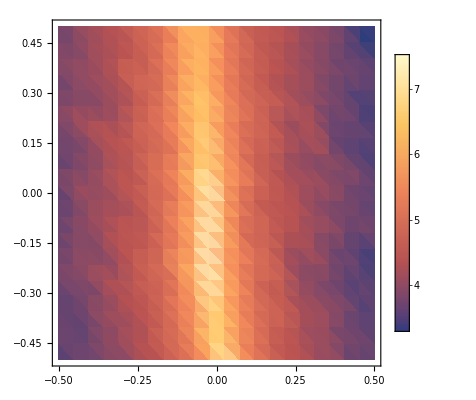

```mathematica
ListDensityPlot[Flatten[dataZ1,2],PlotLegends->True]
```

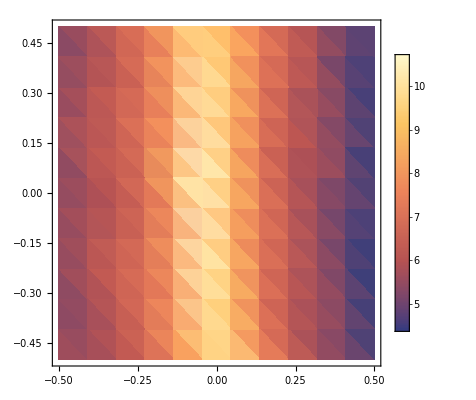

```mathematica
ListDensityPlot[Flatten[dataZ,2],PlotLegends->True]
```

```mathematica
RL results
```

```mathematica
C2, C3 std reward
```

```mathematica
(*the average end point is(mean std):*)
```

```mathematica
(1.9784480697681104,0.0005325501269543725)
(3.3983802834701855,0.00368965178040087)
```

```mathematica
C2 std reward
```

```mathematica
(*the average end point is(mean std):*)
```

```mathematica
(1.9753362936440448,0.0012150231786157634)
(3.4522527573473876,0.017054917688017982)
```